```mathematica
(* one-dimentional particle in a box(between walls at x=0 & x=L);
Subscript[E, n]=(n^2 h^2)/(8 π) 
*)
Clear[x,y];
Ψ[x_,y_]:=2 Sin[Subscript[n, 1] π x] Sin[Subscript[n, 2] π y];
Subscript[n, 1]=1;
Subscript[n, 2]=1;
Plot3D[Ψ[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y],{x,0,1},{y,0,1},AxesLabel->{"x","y","ψ"}]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14}]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->100]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=4;
Subscript[n, 2]=4;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->10]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=4;
Subscript[n, 2]=4;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->100]
```

-Graphics3D-

```mathematica
(* PlotPoints指的是在某个方向上（x或y）取点的个数，在上面两个例子里，可以发现，PlotPoints->100时精度更高，而在图形较简单时不明显 *)
```

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,Mesh->40]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,Mesh->None]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,ColorFunction->"Aquamarine"]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,ColorFunction->"GrayTones"](* 绘制黑白图 *)
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,ColorFunction->"ValentineTones",PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,Mesh->None,PlotStyle->Directive[Pink,Specularity[White,100]]]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,Mesh->None,PlotStyle->Directive[Pink,Specularity[White,10]]]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,Mesh->None,PlotStyle->Directive[Blue,Specularity[White,10]],ViewPoint->{1,1,2}]
```

-Graphics3D-

```mathematica
Subscript[n, 1]=2;
Subscript[n, 2]=2;
Plot3D[Ψ[x,y]^2,{x,0,1},{y,0,1},AxesLabel->{"x","y","prob dens"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,Mesh->None,PlotStyle->Directive[Blue,Specularity[White,10]],ViewPoint->{4,4,2}]
```

-Graphics3D-

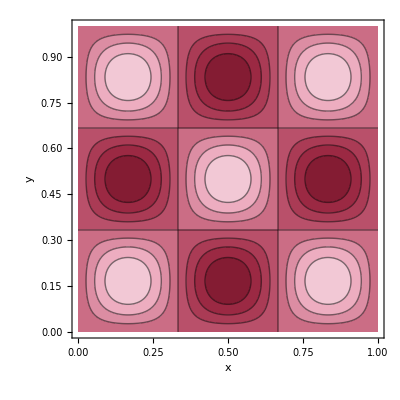

```mathematica
Subscript[n, 1]=3;
Subscript[n, 2]=3;
ContourPlot[Ψ[x,y],{x,0,1},{y,0,1},AxesLabel->{"x","y"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,ColorFunction->"ValentineTones"]
```

```mathematica
Subscript[n, 1]=3;
Subscript[n, 2]=3;
ContourPlot[Ψ[x,y],{x,0,1},{y,0,1},AxesLabel->{"x","y"},BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,ColorFunction->"ValentineTones",Contours->20]
```

-Graphics-

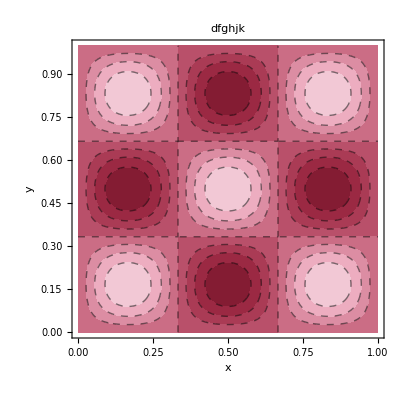

```mathematica
Subscript[n, 1]=3;
Subscript[n, 2]=3;
ContourPlot[Ψ[x,y],{x,0,1},{y,0,1},FrameLabel->{"x","y"},PlotLabel->"dfghjk",BaseStyle->{FontFamily->Helvetica,FontSize->14},PlotPoints->25,ColorFunction->"ValentineTones",ContourStyle->Dashed](* 上面两个ContourPlot中AxesLabel均应改为FrameLabel *)
```

```mathematica
<<PlotLegends`
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
$Packages
```

{PlotLegends`,QuantityUnits`,DocumentationSearch`,CURLInfo`,URLUtilities`,CloudObject`,MailReceiver`,JLink`,Iconize`,UUID`,Security`,CURLLink`Cookies`,OAuthSigning`,CURLLink`HTTP`,CURLLink`,GetFEKernelInit`,SymbolicMachineLearningLoader`,StreamingLoader`,NeuralNetworks`,IconizeLoader`,HTTPHandlingLoader`,CloudObjectLoader`,ResourceLocator`,PacletManager`,System`,Global`}

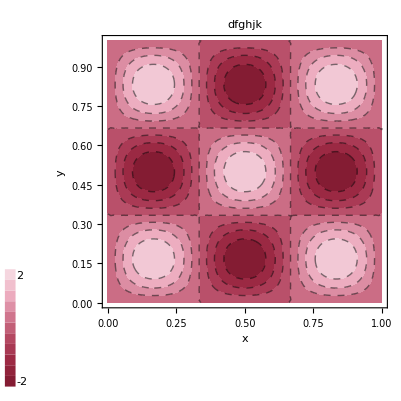

```mathematica
Subscript[n, 1]=3;
Subscript[n, 2]=3;
ShowLegend[ContourPlot[Ψ[x,y],{x,0,1},{y,0,1},FrameLabel->{"x","y"},PlotLabel->"dfghjk",BaseStyle->{FontFamily->Helvetica,FontSize->14},ColorFunction->"ValentineTones",ContourStyle->Dashed],{ColorData["ValentineTones"][1-#1] &,11,"2","-2"}](* 11表示图例层数，“2”，“-2”表示最大值最小值,这里是估计的，下面计算一下 *)
```

```mathematica
MaxValue[{Ψ[x,y],0⩽x⩽1,0⩽y⩽1},{x,y}]
```

2

```mathematica
MinValue[{Ψ[x,y],0⩽x⩽1,0⩽y⩽1},{x,y}]
```

-2

```mathematica
(* 确实如此，事实上可以根据表达式看出 *)
```

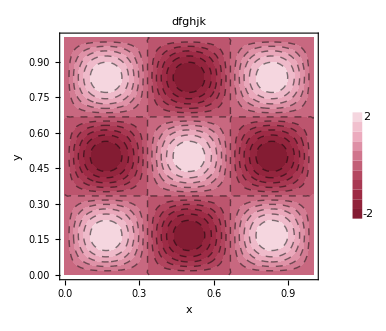

```mathematica
ShowLegend[ContourPlot[Ψ[x,y],{x,0,1},{y,0,1},FrameLabel->{"x","y"},PlotLabel->"dfghjk",BaseStyle->{FontFamily->Helvetica,FontSize->14},ColorFunction->"ValentineTones",Contours->11,ContourStyle->Dashed],{ColorData["ValentineTones"][1-#1] &,11,"2","-2",LegendPosition->{1.1,-0.4}}](* 注意LegendPosition的位置。这两个数字是推荐设置。 *)
```

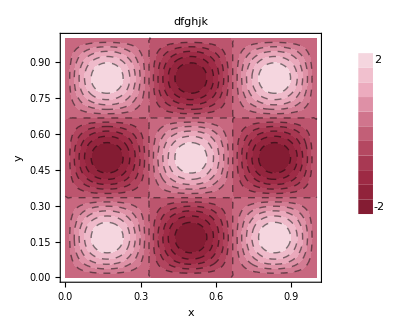

```mathematica
ShowLegend[ContourPlot[Ψ[x,y],{x,0,1},{y,0,1},FrameLabel->{"x","y"},PlotLabel->"dfghjk",BaseStyle->{FontFamily->Helvetica,FontSize->14},ColorFunction->"ValentineTones",Contours->11,ContourStyle->Dashed],{ColorData["ValentineTones"][1-#1] &,11,"2","-2",LegendPosition->{1.1,-0.4},LegendShadow->None,LegendSize->1.2}]
```

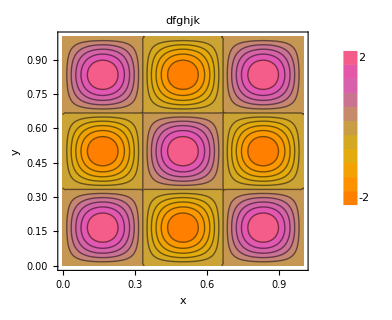

```mathematica
ShowLegend[ContourPlot[Ψ[x,y],{x,0,1},{y,0,1},FrameLabel->{"x","y"},PlotLabel->"dfghjk",BaseStyle->{FontFamily->Helvetica,FontSize->14},Contours->11,ColorFunction->"FruitPunchColors"],{ColorData["FruitPunchColors"][1-#1] &,11,"2","-2",LegendPosition->{1.1,-0.4},LegendShadow->None,LegendSize->1.2}]
```

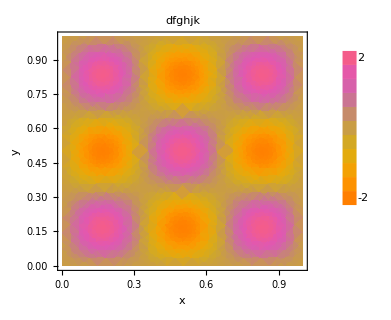

```mathematica
ShowLegend[DensityPlot[Ψ[x,y],{x,0,1},{y,0,1},FrameLabel->{"x","y"},PlotLabel->"dfghjk",BaseStyle->{FontFamily->Helvetica,FontSize->14},ColorFunction->"FruitPunchColors"],{ColorData["FruitPunchColors"][1-#1] &,11,"2","-2",LegendPosition->{1.1,-0.4},LegendShadow->None,LegendSize->1.2}]
```

```mathematica
ShowLegend[ContourPlot[Ψ[x,y],{x,0,1},{y,0,1},FrameLabel->{"x","y"},PlotLabel->"dfghjk",BaseStyle->{FontFamily->Helvetica,FontSize->14},Contours->11,ContourStyle->None,ColorFunction->"FruitPunchColors"],{ColorData["FruitPunchColors"][1-#1] &,11,"2","-2",LegendPosition->{1.1,-0.4},LegendShadow->None,LegendSize->1.2}](* 注意这个图与上个图类似但稍有不同 *)
```

-Graphics-